```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
(*Data in*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805"};
(* old uses 2 data points for harmonic approximation:
filesCh={"harm.C_4685_760","harm.C_4730_1900","harm.C_4759_2500","harm.C_4801_3200","harm.C_4850_3805"};
filesZrh={"harm.Zr_4685_760","harm.Zr_4730_1900","harm.Zr_4759_2500","harm.Zr_4801_3200","harm.Zr_4850_3805"};
*)
(*New harmonic is only bases on a single displacement of 0.01 Angstrom for both Zr and C:*)
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,5}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,5}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,5}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,5}];
```

```mathematica
hZrdata
```

{{{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75}},{{-0.00946,0.7},{0,0},{0,0},{0.00946,0.7}},{{-0.00951,0.67},{0,0},{0,0},{0.00951,0.67}},{{-0.0096,0.62},{0,0},{0,0},{0.0096,0.62}},{{-0.0097,0.56},{0,0},{0,0},{0.0097,0.56}}}

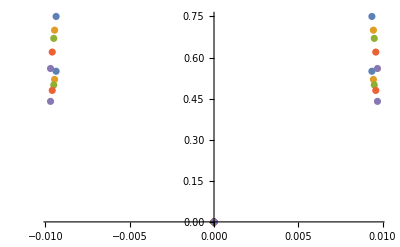

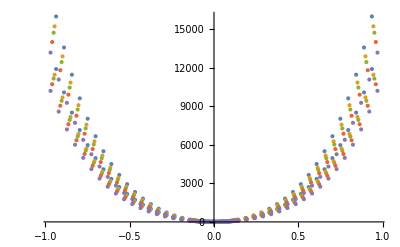

```mathematica
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;

(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,5}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,5}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,5}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,5}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,5}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,5}]

(*Zirconium*)
V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,5}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,5}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,5}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,5}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,5}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,5}]
```

```mathematica
V[1,6,x]
```

{6256.47 x^2+6879.88 x^4+1626.02 x^6,5773.71 x^2+6413.2 x^4+1606.25 x^6,5477.59 x^2+6120.61 x^4+1577.72 x^6,5060.75 x^2+5691.53 x^4+1551.31 x^6,4589.63 x^2+5205.81 x^4+1535.05 x^6}

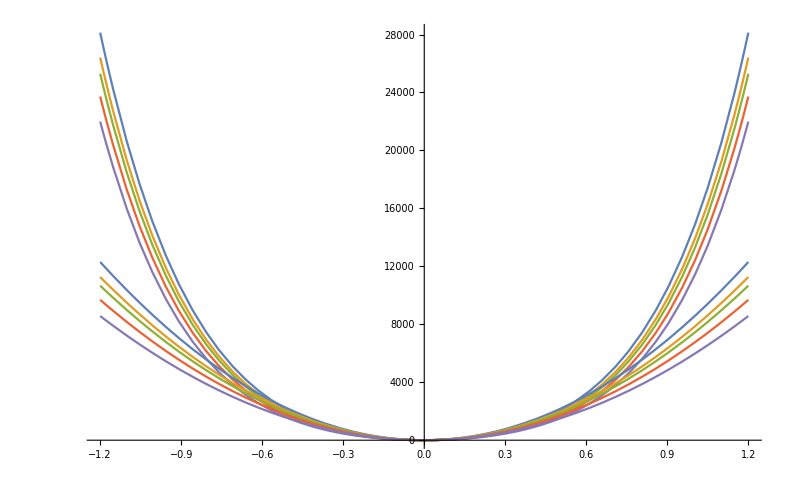

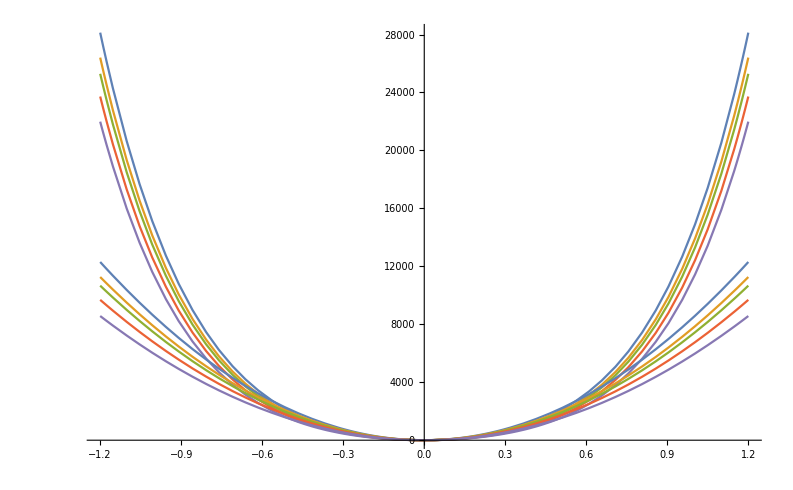

```mathematica
Show[Plot[Evaluate@V[1,6,x],{x,-1.2,1.2},PlotRange->All],Plot[Evaluate@V[2,2,x],{x,-1.2,1.2}]]
Show[Plot[Evaluate@V[1,6,x],{x,-1.2,1.2}],Plot[Evaluate@V[2,2,x],{x,-1.2,1.2}]]
```

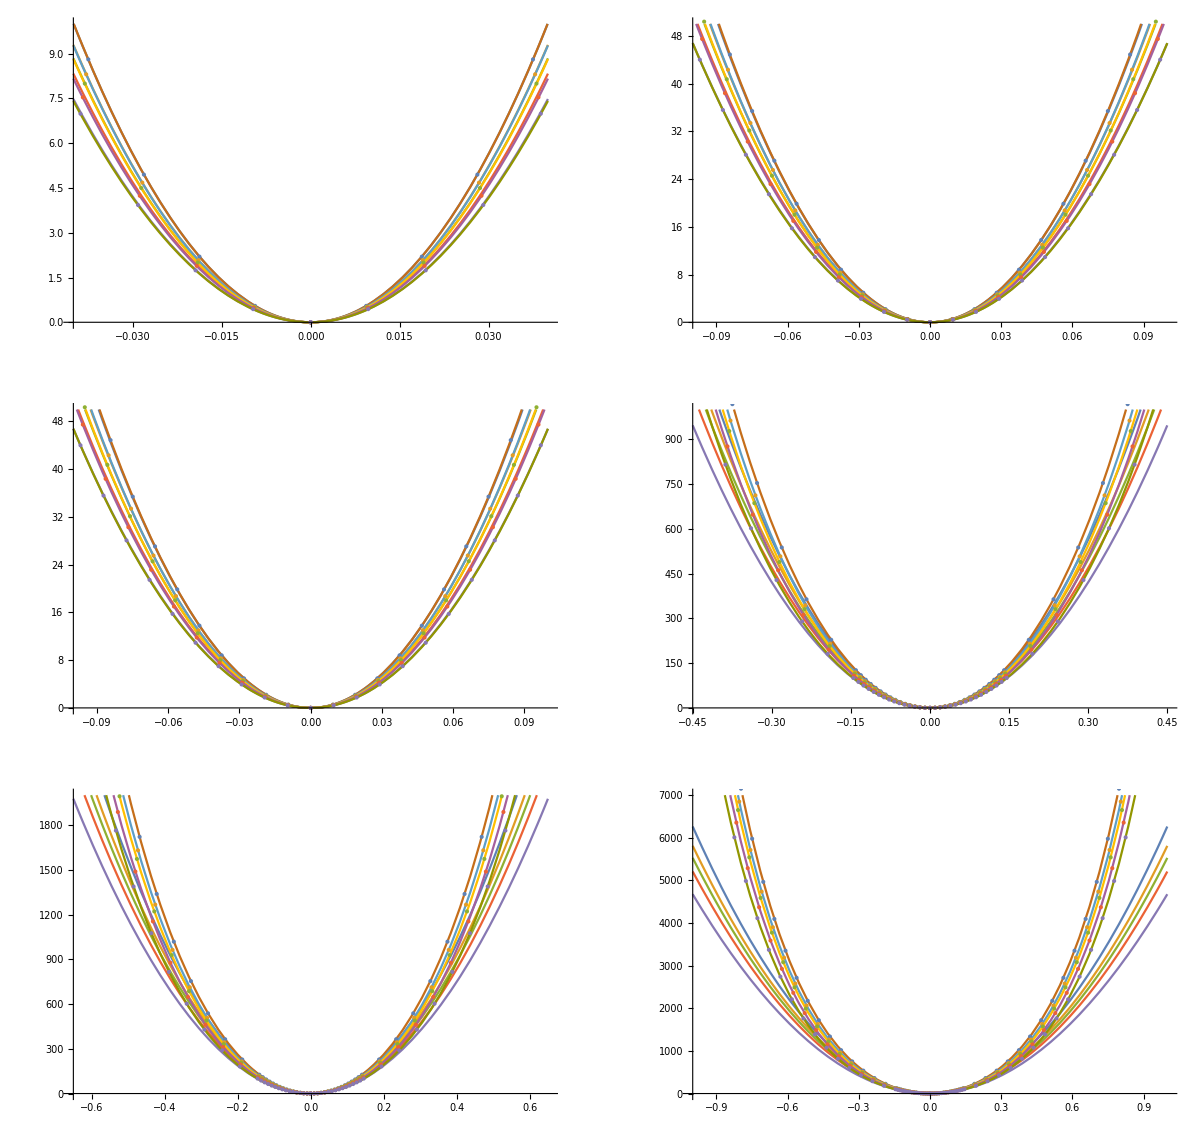

```mathematica
Carbon- look at the fits to examine agreement different length scales;
commonplotinfo={AxesLabel->{"Displacement (Å)","E-E0ref (meV) "}};
P00=With[{B=0.04,H=10},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2=With[{B=0.45,H=1000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3=With[{B=0.65,H=2000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4=With[{B=1,H=7000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00,ListPlot@Cdata],Show[P0,ListPlot@Cdata]},{Show[P1,ListPlot@Cdata],Show[P2,ListPlot@Cdata]},{Show[P3,ListPlot@Cdata],Show[P4,ListPlot@Cdata]}},ImageSize->1200]
```

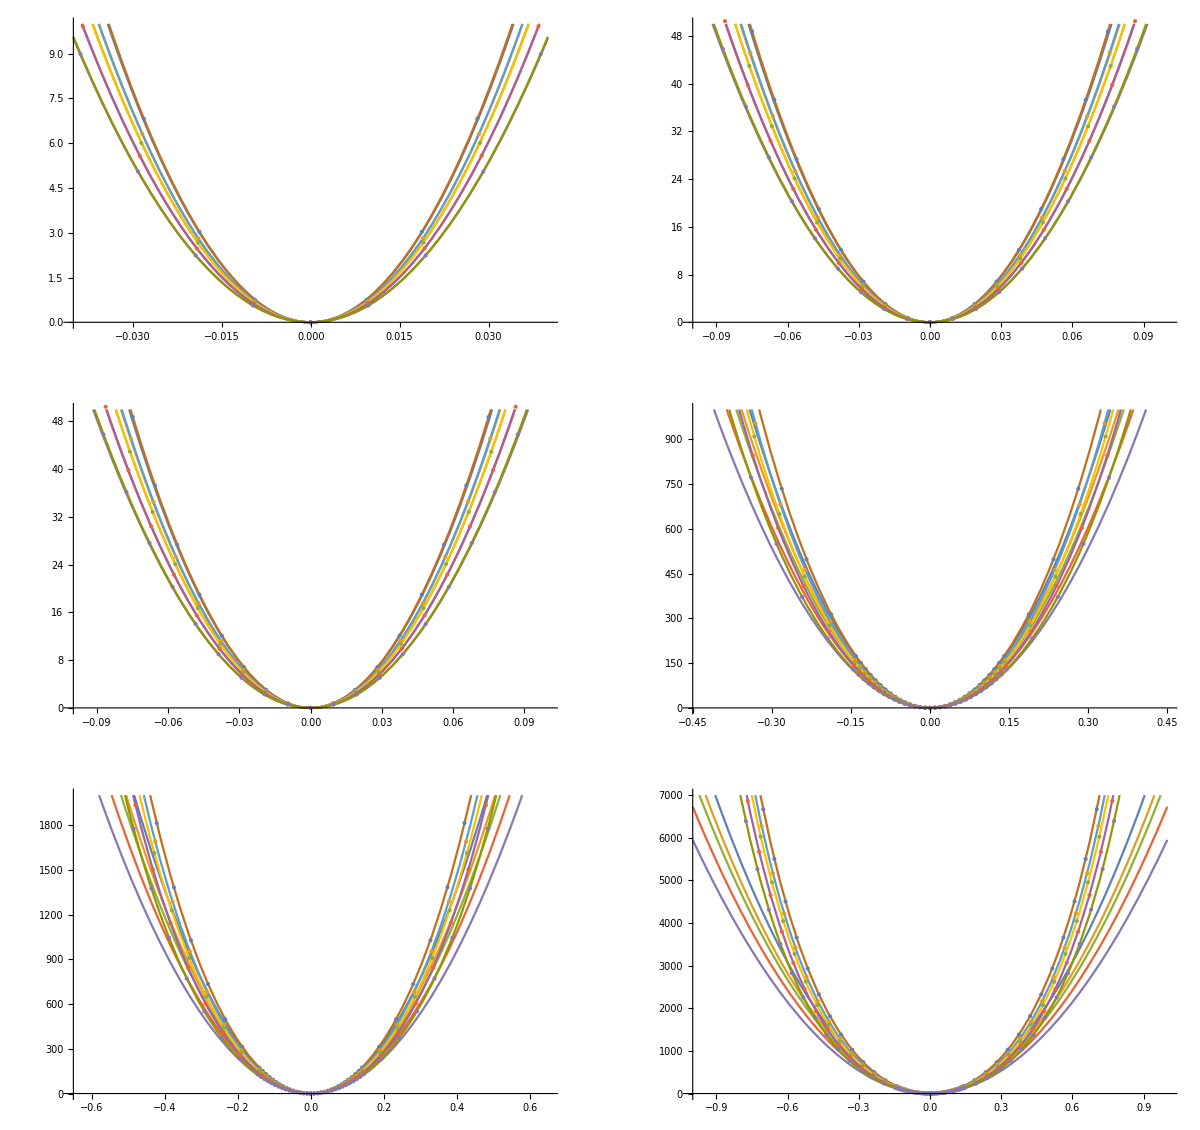

```mathematica
Look at fits at different scales - Zirconium;
P00z=With[{B=0.04,H=10},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2z=With[{B=0.45,H=1000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3z=With[{B=0.65,H=2000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4z=With[{B=1,H=7000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00z,ListPlot@Zrdata],Show[P0z,ListPlot@Zrdata]},{Show[P1z,ListPlot@Zrdata],Show[P2z,ListPlot@Zrdata]},{Show[P3z,ListPlot@Zrdata],Show[P4z,ListPlot@Zrdata]}},ImageSize->1200]
```

```mathematica
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`50."&);
```

```mathematica
Carbon and zirconium - calculate harmonic frequency of fit (as root of prefactor *2 over mass);
(*If the fitted carbon potential is f(x)=A*x*x, let it be equal to standard harmonic expression, f(x)=A*x*x=1/2*m*omega*omega*x*x*)
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,5}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,5}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{6264.46,5810.6,5528.52,5208.33,4676.37}

cOmega0 in meV/Ang**2/AMU is approximately

{32.2978,31.1058,30.3414,29.4497,27.9052}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{8542.44,7821.96,7408.22,6727.43,5951.75}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{13.6852,13.0954,12.7443,12.1447,11.4231}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=200;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,2i,x]*u[x],{i,1,6,1}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,2i,x]*u[x],{i,1,6,1}];
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

```mathematica
Carbon and zirconium eigensystem solution;
(*ℒallc[[harmonic=1,anharmonic=2(quartic),anharmonic=3(6thorder)...]][[volumes1,2,3,4,5]]*)

(*harmonic eigensystems*)
(*Carbon eigensystem*)
eigensysCh=Table[NDEigensystem[ℒallc[[1]][[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,5}];
(*Zironcium eigensystem*)
eigensysZh=Table[NDEigensystem[ℒallz[[1]][[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,5}];

(*anharmonic eigensystem - 6th order*)
(*Carbon eigensystem*)
eigensysC=Table[NDEigensystem[ℒallc[[3]][[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,5}];
(*Zironcium eigensystem*)
eigensysZ=Table[NDEigensystem[ℒallz[[3]][[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,5}];
```

```mathematica
(*eigensysCh[[vol]][[vals/vectors]]*)
(*Carbon harmonic and anharmonic spectrums*)

chrelspectrum=Table[(eigensysCh[[vol]][[1]]/(2eigensysCh[[vol]][[1]][[1]]))/(Table[i-0.5,{i,1,Length[eigensysCh[[1]][[1]]]}]),{vol,1,5}];
crelspectrum=Table[(eigensysC[[vol]][[1]]/(2eigensysC[[vol]][[1]][[1]]))/(Table[i-0.5,{i,1,Length[eigensysC[[1]][[1]]]}]),{vol,1,5}];

(*Zr harmonic and anharmonic spectrums*)
zhrelspectrum=Table[(eigensysZh[[vol]][[1]]/(2eigensysZh[[vol]][[1]][[1]]))/(Table[i-0.5,{i,1,Length[eigensysZh[[1]][[1]]]}]),{vol,1,5}];
zrelspectrum=Table[(eigensysZ[[vol]][[1]]/(2eigensysZ[[vol]][[1]][[1]]))/(Table[i-0.5,{i,1,Length[eigensysZ[[1]][[1]]]}]),{vol,1,5}];
```

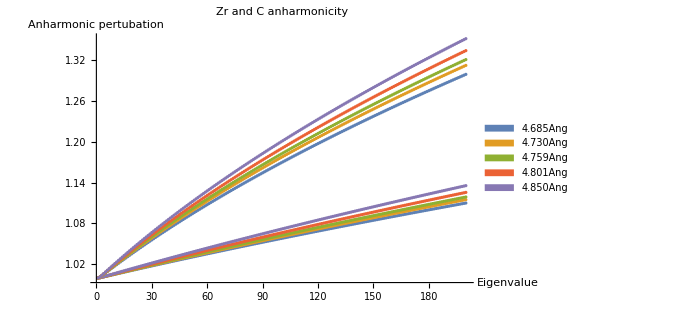

```mathematica
Show[ListPlot[zrelspectrum,PlotLegends->SwatchLegend[{"4.685Ang","4.730Ang","4.759Ang","4.801Ang","4.850Ang"}]],ListPlot[crelspectrum],PlotRange->All,PlotLabel->"Zr and C anharmonicity",AxesLabel->{"Eigenvalue","Anharmonic \npertubation"},ImageSize->500]
```

```mathematica
(*zr anharmonic fits*)
(**)
anhfitz1=Table[Fit[zrelspectrum[[vol]],{1,x},x],{vol,1,5}]
anhfitz2=Table[Fit[zrelspectrum[[vol]],{1, x, x^2},x],{vol,1,5}]
anhfitz3=Table[Fit[zrelspectrum[[vol]],{1, x, x^2,x^3},x],{vol,1,5}]
anhfitz4=Table[Fit[zrelspectrum[[vol]],{1, x, x^2,x^3,x^4},x],{vol,1,5}]
(*Conclusion from different orders of fit to the anharmonic interaction shows quadratic wins*)
Show[Plot[{anhfitz1,anhfitz2},{x,1,250},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
Show[Plot[{anhfitz2,anhfitz3},{x,1,250},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
Show[Plot[{anhfitz2,anhfitz4},{x,1,250},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
```

{1.00158+0.000551982 x,1.00159+0.000577061 x,1.00166+0.000596456 x,1.00183+0.000630322 x,1.00215+0.000679869 x}

{0.999293+0.000619799 x-3.37398×10^-7 x^2,0.999255+0.000646481 x-3.45376×10^-7 x^2,0.999231+0.000668639 x-3.5912×10^-7 x^2,0.999195+0.000708612 x-3.89503×10^-7 x^2,0.999152+0.000768785 x-4.42372×10^-7 x^2}

{0.999127+0.000629551 x-4.58386×10^-7 x^2+4.01289×10^-10 x^3,0.999089+0.000656229 x-4.66312×10^-7 x^2+4.01115×10^-10 x^3,0.999058+0.000678829 x-4.85554×10^-7 x^2+4.19352×10^-10 x^3,0.999003+0.00071998 x-5.30546×10^-7 x^2+4.67804×10^-10 x^3,0.99892+0.000782473 x-6.12195×10^-7 x^2+5.63259×10^-10 x^3}

{0.999132+0.000629109 x-4.4856×10^-7 x^2+3.25369×10^-10 x^3+1.88856×10^-13 x^4,0.999095+0.000655667 x-4.53817×10^-7 x^2+3.04576×10^-10 x^3+2.40149×10^-13 x^4,0.999064+0.000678273 x-4.73171×10^-7 x^2+3.23678×10^-10 x^3+2.37994×10^-13 x^4,0.999007+0.000719526 x-5.20437×10^-7 x^2+3.89704×10^-10 x^3+1.94279×10^-13 x^4,0.998921+0.000782322 x-6.08836×10^-7 x^2+5.37308×10^-10 x^3+6.45556×10^-14 x^4}

```mathematica
(*carbon anharmonic fits*)
anhfitc1=Table[Fit[crelspectrum[[vol]],{1,x},x],{vol,1,5}]
anhfitc2=Table[Fit[crelspectrum[[vol]],{1, x, x^2},x],{vol,1,5}]
anhfitc3=Table[Fit[crelspectrum[[vol]],{1, x, x^2,x^3},x],{vol,1,5}]
anhfitc4=Table[Fit[crelspectrum[[vol]],{1, x, x^2,x^3,x^4},x],{vol,1,5}]

(*Linear vs quadratic fits to anharmonic perturbation*)
(*Conclusion from different orders of fit to the anharmonic interaction shows quadratic wins*)
Show[Plot[{anhfitc1,anhfitc2},{x,1,250},PlotRange->All],ListPlot[crelspectrum],ImageSize->1200];
```

{1.01412+0.00148091 x,1.01506+0.00154526 x,1.01572+0.00158693 x,1.01664+0.00165126 x,1.01781+0.00173727 x}

{1.00018+0.00189505 x-2.06038×10^-6 x^2,1.00029+0.00198395 x-2.18253×10^-6 x^2,1.00038+0.00204251 x-2.26653×10^-6 x^2,1.00049+0.0021309 x-2.38628×10^-6 x^2,1.00062+0.00224795 x-2.54067×10^-6 x^2}

{0.997741+0.00203865 x-3.84208×10^-6 x^2+5.90945×10^-9 x^3,0.997664+0.00213879 x-4.10359×10^-6 x^2+6.3717×10^-9 x^3,0.997617+0.00220531 x-4.28639×10^-6 x^2+6.69936×10^-9 x^3,0.99754+0.00230469 x-4.54249×10^-6 x^2+7.15164×10^-9 x^3,0.997435+0.0024356 x-4.86881×10^-6 x^2+7.72185×10^-9 x^3}

{0.997267+0.00208481 x-4.86948×10^-6 x^2+1.38473×10^-8 x^3-1.97459×10^-11 x^4,0.99714+0.00218976 x-5.23823×10^-6 x^2+1.51381×10^-8 x^3-2.18069×10^-11 x^4,0.997057+0.00225979 x-5.49902×10^-6 x^2+1.60683×10^-8 x^3-2.33059×10^-11 x^4,0.996931+0.00236393 x-5.86113×10^-6 x^2+1.73396×10^-8 x^3-2.53433×10^-11 x^4,0.996765+0.00250077 x-6.31939×10^-6 x^2+1.89293×10^-8 x^3-2.78792×10^-11 x^4}

```mathematica
fanhc[x_]:=anhfitc4/.x->x
fanhz[x_]:=anhfitz4/.x->x
cOmega0
zOmega0
fanhcOmega[x_]:=anhfitc4*cOmega0/.x->x
fanhzOmega[x_]:=anhfitz4*zOmega0/.x->x
```

{32.2978,31.1058,30.3414,29.4497,27.9052}

{13.6852,13.0954,12.7443,12.1447,11.4231}

```mathematica
s0=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,10},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s1=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,50},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s2=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,200},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s3=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,300},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum,PlotLegends->SwatchLegend[{"4.685Ang","4.730Ang","4.759Ang","4.801Ang","4.850Ang"}]]];
GraphicsGrid[{{s0,s1,s2,s3}}]
```

-Graphics-

```mathematica
free[T_,spectrumZ_,spectrumC_,maxEigen_]:=-K2meV*1.5*T*Log[{Total[Exp[-2*Table[((0.5+x)*(spectrumZ)),{x,0,maxEigen}]/(K2meV*T)]],Total[Exp[-2*Table[((0.5+x)*(spectrumC)),{x,0,maxEigen}]/(K2meV*T)]]}]
```

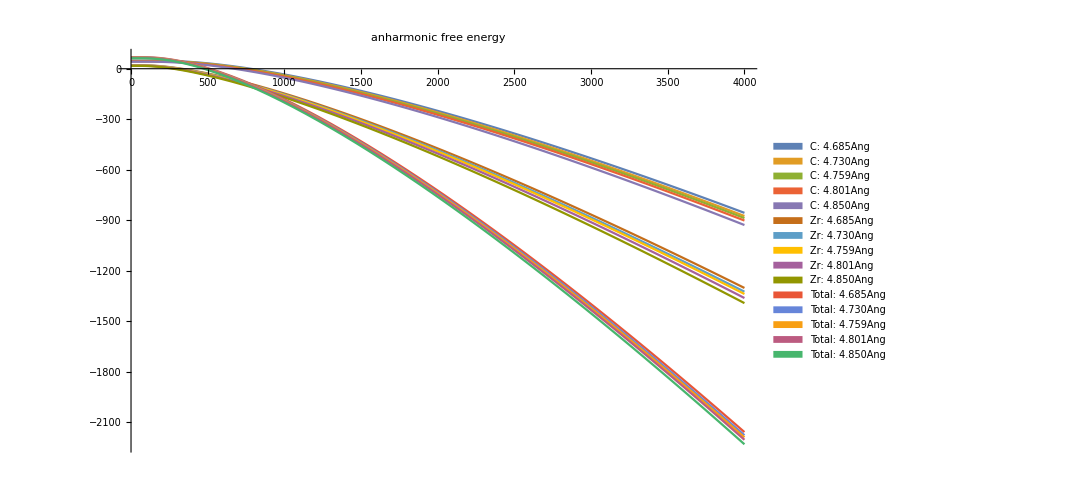

```mathematica
Plot[{Evaluate@(free[T,fanhcOmega[x],fanhzOmega[x],200]),Evaluate@Total@(free[T,fanhcOmega[x],fanhzOmega[x][[1]],200])}
,{T,1,4000},ImageSize->800,PlotLabel->"anharmonic free energy",PlotLegends->SwatchLegend[{"C: 4.685Ang","C: 4.730Ang","C: 4.759Ang","C: 4.801Ang","C: 4.850Ang","Zr: 4.685Ang","Zr: 4.730Ang","Zr: 4.759Ang","Zr: 4.801Ang","Zr: 4.850Ang","Total: 4.685Ang","Total: 4.730Ang","Total: 4.759Ang","Total: 4.801Ang","Total: 4.850Ang"}]]
```

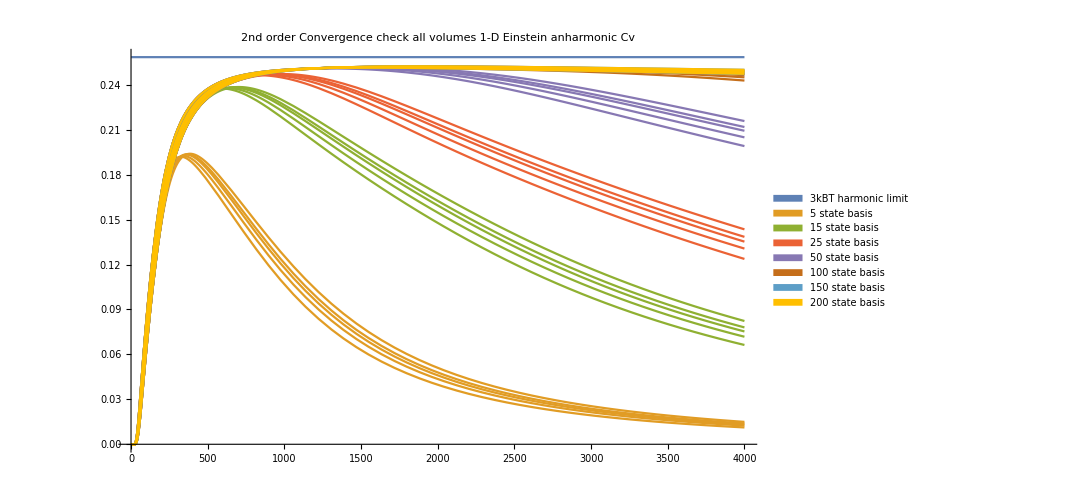

```mathematica
Plot[{K2meV*3,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],5],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],15],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],25],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],50],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],100],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],150],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"2nd order Convergence check all volumes 1-D Einstein anharmonic Cv",PlotLegends->SwatchLegend[{"3kBT harmonic limit","5 state basis","15 state basis","25 state basis","50 state basis","100 state basis","150 state basis","200 state basis"}]]
```

```mathematica
(*All volumes anharmonic harmonic heat capcity comparison 30 basis*)
pha0=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],30],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,30],T],T]])/.T->t},{t,1,4000},PlotLabel->"30basis"];
(**PlotLegends->SwatchLegend[{"3kB","anharmonic 4.685Ang","anharmonic 4.730Ang","anharmonic 4.759Ang","anharmonic 4.801Ang","anharmonic 4.850Ang","harmonic 4.685Ang","harmonic 4.730Ang","harmonic 4.759Ang","harmonic 4.801Ang","harmonic 4.850Ang"}*)
(*All volumes anharmonic harmonic heat capcity comparison 100 basis*)
pha1=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],100],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,100],T],T]])/.T->t},{t,1,4000},PlotLabel->"100basis"];
(*All volumes anharmonic harmonic heat capcity comparison 200 basis*)
pha2=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,200],T],T]])/.T->t},{t,1,4000},PlotLabel->"200basis"];
(*(*All volumes anharmonic harmonic heat capcity comparison 300 basis - too big*)
pha3=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],300],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,300],T],T]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"3kB","anharmonic all volumes","harmonic all volumes"}],PlotLabel->"300basis"]*)
```

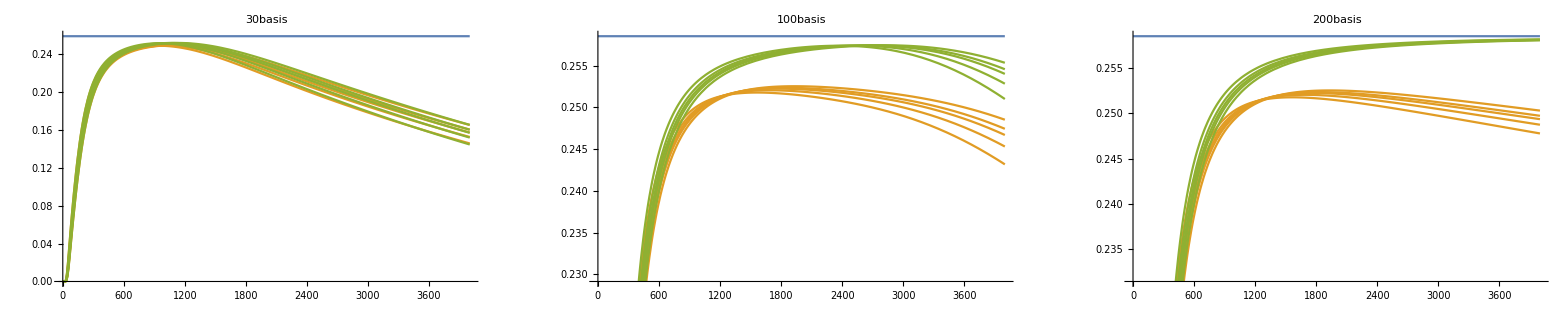

```mathematica
GraphicsGrid[{{pha0,pha1,pha2}},ImageSize->2500]
```

```mathematica
cvPerturb=(T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]-T*D[-D[free[T,cOmega0,zOmega0,200],T],T]);
```

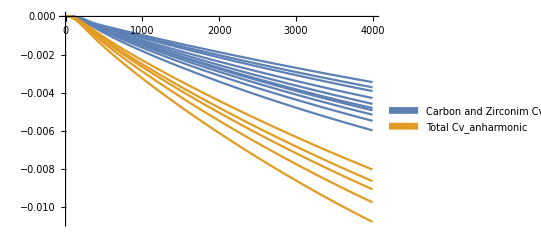

```mathematica
Plot[{Evaluate@cvPerturb/.T->t,Total[cvPerturb]/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"Carbon and Zirconim Cv_anharmonic","Total Cv_anharmonic"}]]
```

```mathematica
(*Import QHA dS/dV and dV/dT to convert Cv to Cp*)
```

```mathematica
temps={760,1900,2500,3200,3805};
anCv=Total[cvPerturb]/.T->temps
```

{{-0.00173617,-0.00421408,-0.00538359,-0.00666076,-0.00769681},{-0.00189362,-0.0045626,-0.005817,-0.00718206,-0.00828475},{-0.00200729,-0.0048118,-0.00612547,-0.00755119,-0.00869905},{-0.00219144,-0.00521483,-0.00662332,-0.00814536,-0.00936319},{-0.00247929,-0.00583321,-0.00738212,-0.00904431,-0.0103597}}

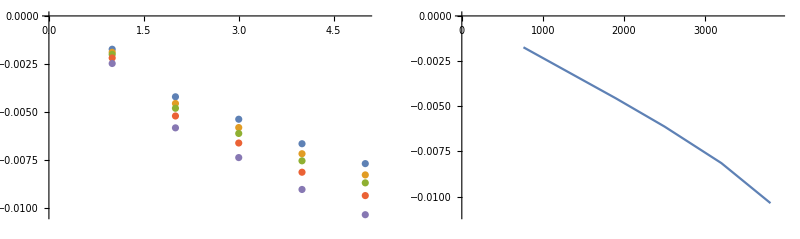

```mathematica
GraphicsGrid[{{ListPlot@anCv,ListPlot[Transpose@{temps,Table[anCv[[i]][[i]],{i,1,5}]},PlotRange->{{0,3900},{-0.011,0}},Joined->True]}},ImageSize->800]
```

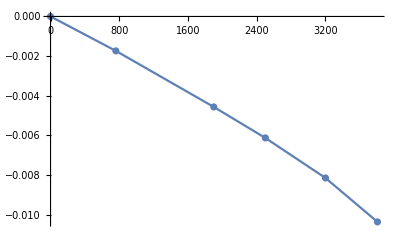

-0.0000515612-1.99149×10^-6 T-1.8186×10^-10 T^2

```mathematica
anCvdata=Partition[Flatten@{{0,0},Transpose[{temps,Table[anCv[[i]][[i]],{i,1,5}]}]},2];
Show[ListPlot[anCvdata],ListPlot[anCvdata,Joined->True]]
Cvanfit=Fit[anCvdata,{1,T,T^2},T]
```

```mathematica
(*Cp=Cv+T*dV/dT*dS/dV*)
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
qhaNormal={"QHA_normal/e-v.dat","QHA_normal/volume_expansion.dat","QHA_normal/volume-temperature.dat","QHA_normal/gruneisen-temperature.dat","QHA_normal/gibbs-temperature.dat","QHA_normal/bulk_modulus-temperature.dat","QHA_normal/Cp-temperature.dat","QHA_normal/dsdv-temperature.dat"};
normal=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,1,8}];
```

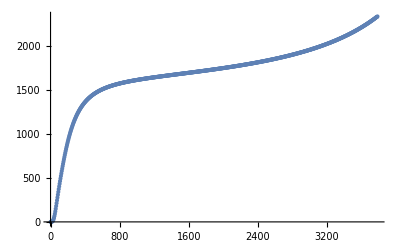

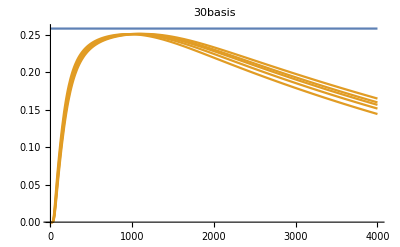

```mathematica
ListPlot[normal[[7]]]
Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,30],T],T]])/.T->t},{t,1,4000},PlotLabel->"30basis"]
```

```mathematica
kjmol2evatom=1/(96.487*64);
qhaCpeVatom=Transpose[{Transpose[normal[[7]]][[1]],Transpose[normal[[7]]][[2]]*kjmol2evatom}];
interQhaCp[T_]:=Interpolation[qhaCpeVatom][T]
```

```mathematica
harmCv[T_]:=1.5*(K2meV*((((2cOmega0[[1]]))/(K2meV*T))^2)*Exp[((2cOmega0[[1]]))/(K2meV*T)]/((Exp[((2cOmega0[[1]]))/(K2meV*T)]-1)^2)+K2meV*((((2zOmega0[[1]]))/(K2meV*T))^2)*Exp[((2zOmega0[[1]]))/(K2meV*T)]/((Exp[((2zOmega0[[1]]))/(K2meV*T)]-1)^2))
```

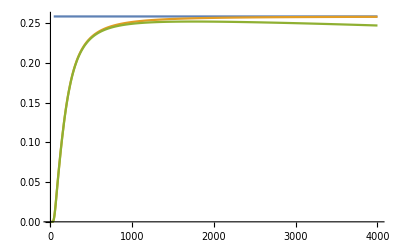

```mathematica
Plot[{3K2meV,harmCv[T],harmCv[T]+Cvanfit/.T->T},{T,1,4000},PlotRange->All]
```

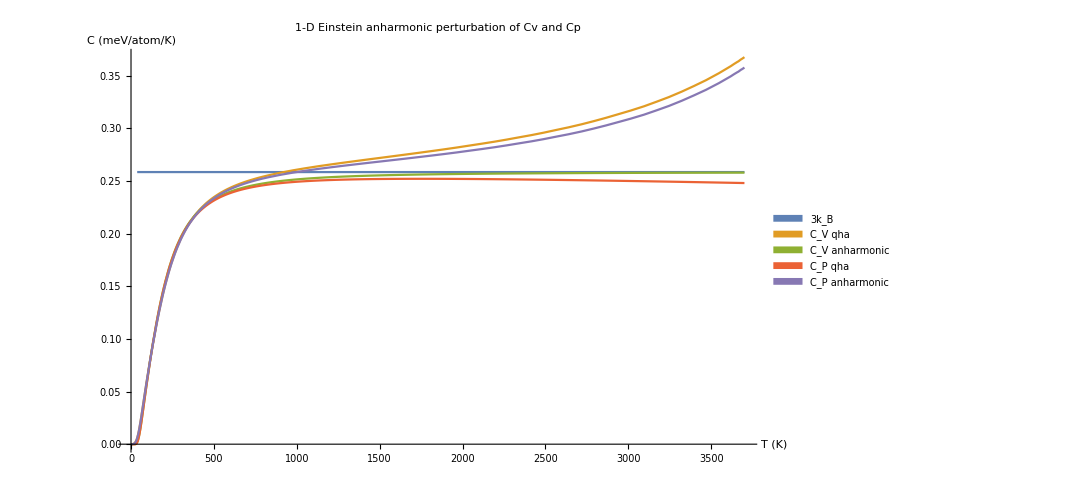

```mathematica
(*Plot the volume dependent anharmonic pertubuation of Cv and Cp*)
Plot[{3K2meV,interQhaCp[T],harmCv[T],harmCv[T]+Cvanfit/.T->T,interQhaCp[T]+Cvanfit/.T->T},{T,1,3700},PlotRange->All,PlotLabel->"1-D Einstein anharmonic perturbation of Cv and Cp",PlotLegends->SwatchLegend[{"3k_B","C_V qha","C_V anharmonic","C_P qha","C_P anharmonic"}],ImageSize->800,AxesLabel->{"T (K)","C (meV/atom/K)"}]
```

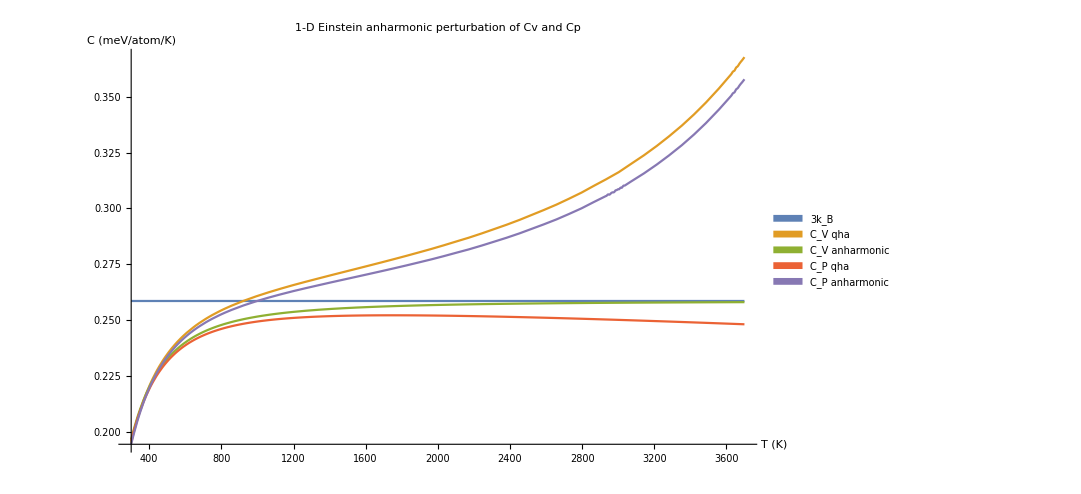

```mathematica
(*Plot the volume dependent anharmonic pertubuation of Cv and Cp*)
Plot[{3K2meV,interQhaCp[T],harmCv[T],harmCv[T]+Cvanfit/.T->T,interQhaCp[T]+Cvanfit/.T->T},{T,300,3700},PlotRange->All,PlotLabel->"1-D Einstein anharmonic perturbation of Cv and Cp",PlotLegends->SwatchLegend[{"3k_B","C_V qha","C_V anharmonic","C_P qha","C_P anharmonic"}],ImageSize->800,AxesLabel->{"T (K)","C (meV/atom/K)"}]
```

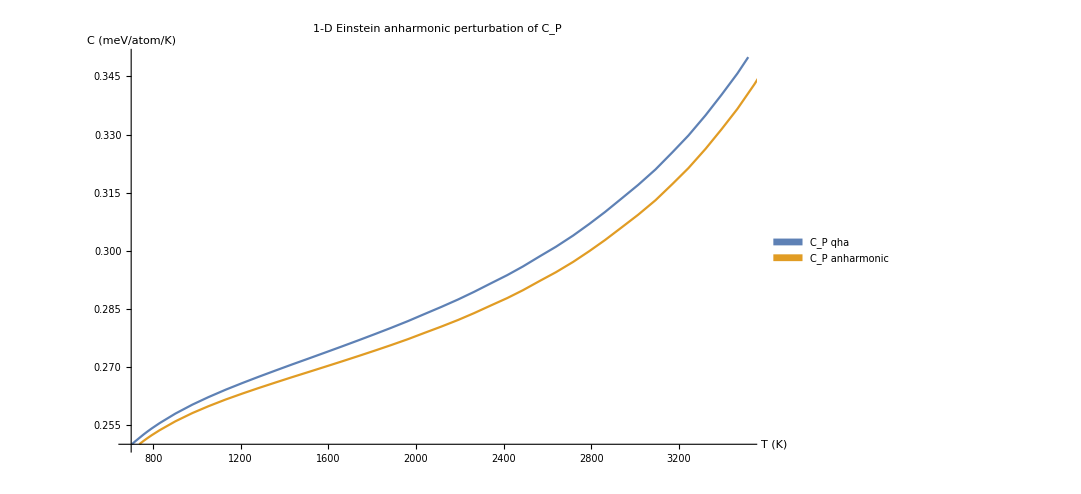

```mathematica
(*Plot the volume dependent anharmonic pertubuation of Cv and Cp*)
Plot[{interQhaCp[T],interQhaCp[T]+Cvanfit/.T->T},{T,1,3700},PlotLabel->"1-D Einstein anharmonic perturbation of C_P",PlotLegends->SwatchLegend[{"C_P qha","C_P anharmonic"}],ImageSize->800,AxesLabel->{"T (K)","C (meV/atom/K)"},PlotRange->{{700,3500},{0.25,0.35}}]
```